{{0,0,1,0},{0,0,1,1},{1,1,1,0},{0,0,0,0}}

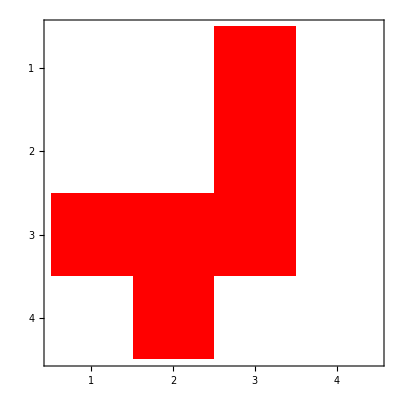
-Graphics-2 | 2 | 0 | 1
2 | 2 | 0 | 1
0 | 0 | 0 | 1
1 | 0 | 2 | 22 | 2 | 0 | 4
2 | 2 | 0 | 4
0 | 0 | 0 | 4
1 | 0 | 1 | 43 | 3 | 0 | 4
3 | 3 | 0 | 4
0 | 0 | 0 | 4
1 | 0 | 2 | 5

```mathematica
matrix = {
{0, 0, 1, 0},
{0, 0, 1, 0},
{1, 1, 1, 0},
{0, 1, 0, 0}
};
reversedMatrix = Table[Table[matrix[[i,j]], {i, Length@matrix}], {j,Length@matrix}]
lineRules = {
{0, 0, 0, 0}->{4, 4, 4, 4},
{1, 0, 0, 0}->{0, 3, 3, 3},
{0, 1, 0, 0}->{1, 0, 2, 2},
{0, 0, 1, 0}->{2, 2, 0, 1},
{0, 0, 0, 1}->{3, 3, 3, 0},
{1, 1, 0, 0}->{0, 0,2, 2},
{1, 0, 1, 0}->{0, 1, 0, 1},
{1, 0, 0, 1}->{0, 2, 2, 0},
{0, 1, 1, 0} ->{1, 0, 0, 1},
{0, 1, 0, 1}->{1, 0, 1, 0},
{0, 0, 1, 1}->{2, 2, 0, 0},
{1, 1, 1, 0}->{0, 0, 0, 1}
};
lineContinuity = matrix /.lineRules;
colContinuity = reversedMatrix/.lineRules;
colContinuity= Table[Table[colContinuity[[i,j]], {i, Length@colContinuity}], {j,Length@colContinuity}];
sumContinuity = lineContinuity+colContinuity;
sumContinuity = sumContinuity/.{0->0, x_Integer/;x>0->x-1};

Overlay[{
MatrixPlot[matrix, ColorRules->{0->White, 1->Red}], 
Grid[lineContinuity, ItemSize->{7, 7}],
Grid[colContinuity, ItemSize->{6.5, 6.5}, ItemStyle->Blue],
Grid[sumContinuity, ItemSize->{7.5, 7.5}, ItemStyle->Green]
}, 
ImageSize->Large]
```

```mathematica
Options@Grid
```

{Alignment→{Center,Baseline},AllowedDimensions→Automatic,AllowScriptLevelChange→True,AutoDelete→False,Background→None,BaselinePosition→Automatic,BaseStyle→{},DefaultBaseStyle→Grid,DefaultElement→□,DeleteWithContents→True,Dividers→{},Editable→Automatic,Frame→None,FrameStyle→Automatic,ItemSize→Automatic,ItemStyle→None,Selectable→Automatic,Spacings→Automatic,StripOnInput→False}